# Practical 2

HARIOM (20201022)

Q1. Find all the solutions of the equation z^3=8i and represent these geometrically.

The roots of the given equation are given by

-2 ⅈ
ⅈ+√3
ⅈ-√3

The roots lie on the circle |z|=2 and graphically represented as

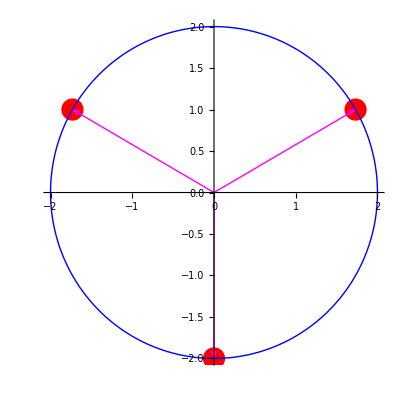

```mathematica
u:=z/.ComplexExpand[Solve[z^3==8*I,z]];
Print["The roots of the given equation are given by"];
Column[Table[u[[i]],{i,1,3}]]
Print["The roots lie on the circle |z|=2 and graphically represented as"]
a:=ListPlot[Table[{Re[u[[i]]],Im[u[[i]]]},{i,1,3}],AspectRatio->Automatic,PlotStyle->{Red,PointSize[0.04]}];
b:=Table[Graphics[{Thick,Magenta,Arrow[{{0,0},{Re[u[[i]]],Im[u[[i]]]}}]}],{i,1,3}];
c:=ParametricPlot[{2*Cos[t],2*Sin[t]},{t,0,2*Pi},PlotStyle->{Thick,Blue}];
Show[a,b,c,PlotRange-> 2]
```

Q2. Find all the solutions of the equation z^4=-16  and represent these geometrically.

The roots of the given equation are given by

(-1-ⅈ) √2
(1+ⅈ) √2
(1-ⅈ) √2
(-1+ⅈ) √2

The roots lie on the circle |z|=2 and graphically represented as

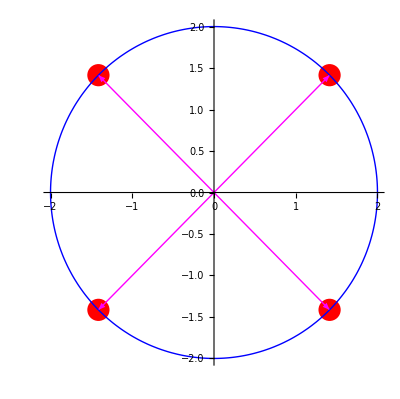

```mathematica
u:=z/.ComplexExpand[Solve[z^4==-16,z]];
Print["The roots of the given equation are given by"];
Column[Table[u[[i]],{i,1,4}]]
Print["The roots lie on the circle |z|=2 and graphically represented as"]
a:=ListPlot[Table[{Re[u[[i]]],Im[u[[i]]]},{i,1,4}],AspectRatio->Automatic,PlotStyle->{Red,PointSize[0.04]}];
b:=Table[Graphics[{Thick,Magenta,Arrow[{{0,0},{Re[u[[i]]],Im[u[[i]]]}}]}],{i,1,4}];
c:=ParametricPlot[{2*Cos[t],2*Sin[t]},{t,0,2*Pi},PlotStyle->{Thick,Blue}];
Show[a,b,c,PlotRange-> 2]
```

Q3. Find all the solutions of the equation z^5=-32i  and represent these geometrically.

The roots of the given equation are given by

-2 ⅈ
ⅈ (1/2-(√5)/2)-2 √(5/8+(√5)/8)
2 √(5/8-(√5)/8)+ⅈ (1/2+(√5)/2)
-2 √(5/8-(√5)/8)+ⅈ (1/2+(√5)/2)
ⅈ (1/2-(√5)/2)+2 √(5/8+(√5)/8)

The roots lie on the circle |z|=2 and graphically represented as

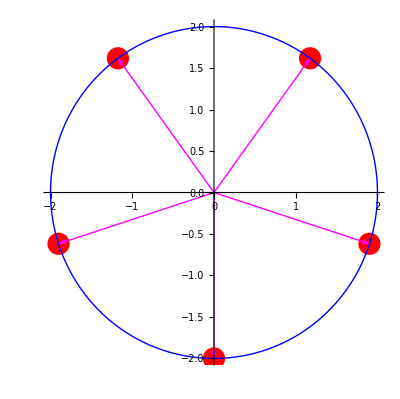

```mathematica
u:=z/.ComplexExpand[Solve[z^5==-32*I,z]];
Print["The roots of the given equation are given by"];
Column[Table[u[[i]],{i,1,5}]]
Print["The roots lie on the circle |z|=2 and graphically represented as"]
a:=ListPlot[Table[{Re[u[[i]]],Im[u[[i]]]},{i,1,5}],AspectRatio->Automatic,PlotStyle->{Red,PointSize[0.04]}];
b:=Table[Graphics[{Thick,Magenta,Arrow[{{0,0},{Re[u[[i]]],Im[u[[i]]]}}]}],{i,1,5}];
c:=ParametricPlot[{2*Cos[t],2*Sin[t]},{t,0,2*Pi},PlotStyle->{Thick,Blue}];
Show[a,b,c,PlotRange-> 2]
```

Q4. Find all the solutions of the equation z^6=-i  and represent these geometrically.

The roots of the given equation are given by

-(√(3/2))/2-1/(2 √2)+ⅈ (-(√(3/2))/2+1/(2 √2))
(√(3/2))/2+1/(2 √2)+ⅈ ((√(3/2))/2-1/(2 √2))
-(√(3/2))/2+1/(2 √2)+ⅈ (-(√(3/2))/2-1/(2 √2))
(√(3/2))/2-1/(2 √2)+ⅈ ((√(3/2))/2+1/(2 √2))
(1-ⅈ)/(√2)
-(1-ⅈ)/(√2)

The roots lie on the circle |z|=2 and graphically represented as

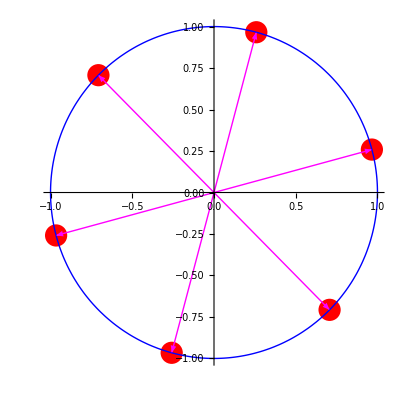

```mathematica
u:=z/.ComplexExpand[Solve[z^6==I,z]];
Print["The roots of the given equation are given by"];
Column[Table[u[[i]],{i,1,6}]]
Print["The roots lie on the circle |z|=2 and graphically represented as"]
a:=ListPlot[Table[{Re[u[[i]]],Im[u[[i]]]},{i,1,6}],AspectRatio->Automatic,PlotStyle->{Red,PointSize[0.04]}];
b:=Table[Graphics[{Thick,Magenta,Arrow[{{0,0},{Re[u[[i]]],Im[u[[i]]]}}]}],{i,1,6}];
c:=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->{Thick,Blue}];
Show[a,b,c,PlotRange-> 1.25]
```